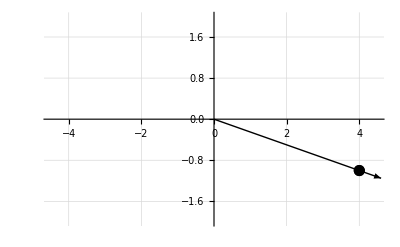

point.png

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
ListPlot[{{4,-1}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Arrow[{{0,0},1.15{4,-1}}]}],
PlotRange->{{-4.5,4.5},{-2,2}},GridLines->Automatic]
Export["point.png",%]
```

121 °

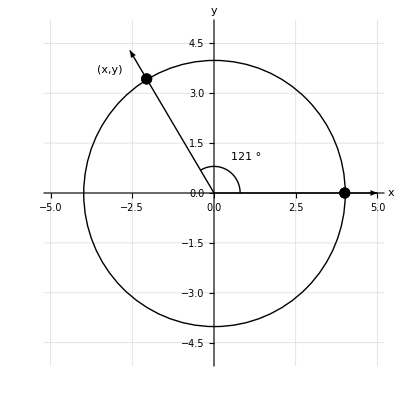

circle.png

```mathematica
r=4;
θ=121*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.6,(r+1) Sin[θ]-0.6}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[θ,Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],

PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->{Medium,Italic}]
Export["circle.png",%]
```

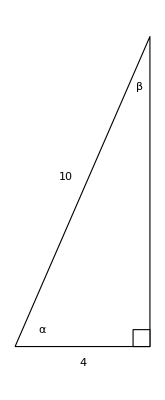

triangle1.png

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{4,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Text[Style[10,Large],{1.5,5}]}],
Graphics[{Text[Style[4,Large],{2,-0.5}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export["triangle1.png",%]
```

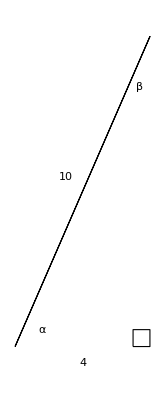

triangle2.png

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{7Cos[ArcSin[1]],0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Text[Style[10,Large],{1.5,5}]}],
Graphics[{Text[Style[4,Large],{2,-0.5}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export["triangle2.png",%]
```

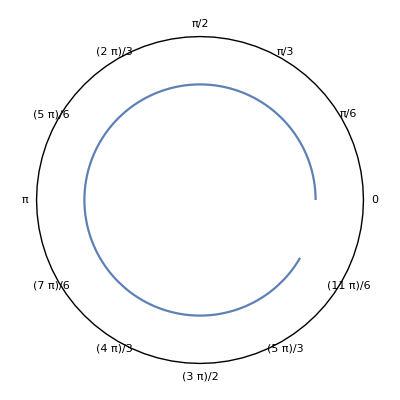

```mathematica
SetDirectory[NotebookDirectory[]];
```

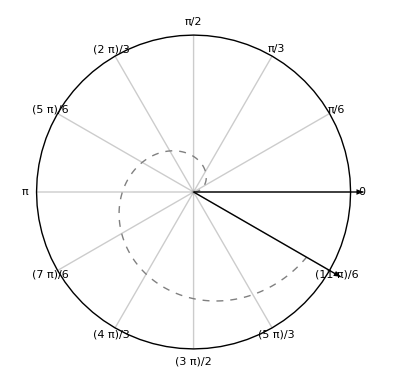

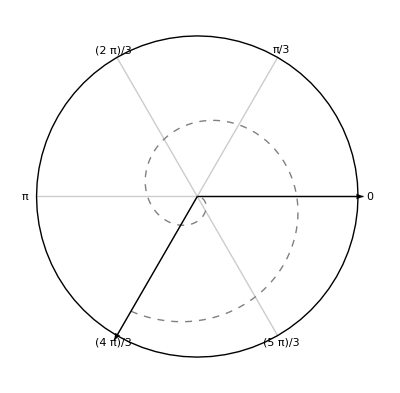

```mathematica
θ=11Pi/6;
Show[PolarPlot[{t/5},{t,0,θ},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/6,Pi/6}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/6,Pi/6}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ 1.5Cos[θ],1.5 Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{1.5,0}}]}]]
Export["ang1.png",%];

θ=-8Pi/3;
Show[PolarPlot[{-t/7},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ 1.5Cos[θ],1.5 Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{1.5,0}}]}]]
Export["ang2.png",%];
```

```mathematica
Drop[Table[i,{i,0,2 Pi,Pi/6}],-1]
```

{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{100,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Text[Style[10,Large],{1.5,5}]}],
Graphics[{Text[Style[4,Large],{2,-0.5}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export["cell.png",%]
```

-Graphics-

cell.png

```mathematica
Tan[40*Degree]*100.
```

83.91

```mathematica
119-84
```

35

```mathematica
4Cos[121*Degree]//N
```

-2.06015

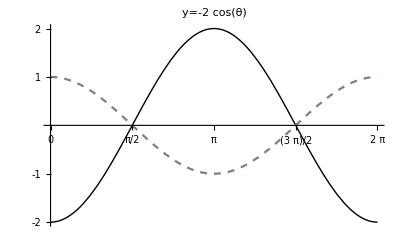

g1.png

```mathematica
Show[
Plot[-2Cos[t],{t,0,2Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
Ticks->{Table[k Pi/2,{k,0,4}],{-2,-1,1,2}},PlotLabel->HoldForm[y=-2Cos[θ]]]
Export["g1.png",%]
```

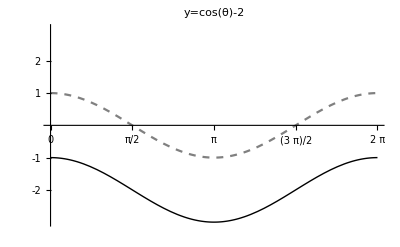

g2.png

```mathematica
Show[
Plot[Cos[t]-2,{t,0,2Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,2Pi},{-3,3}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/2,{k,0,4}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Cos[θ]-2]]
Export["g2.png",%]
```

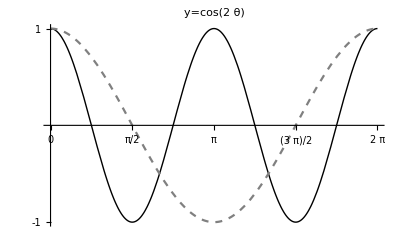

g3.png

```mathematica
Show[
Plot[Cos[2t],{t,0,2Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,2Pi},{-1,1}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/4,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Cos[2θ]]]
Export["g3.png",%]
```

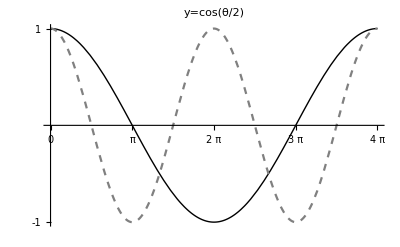

g4.png

```mathematica
Show[
Plot[Cos[t/2],{t,0,4Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,4Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,4Pi},{-1,1}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/2,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Cos[θ/2]]]
Export["g4.png",%]
```

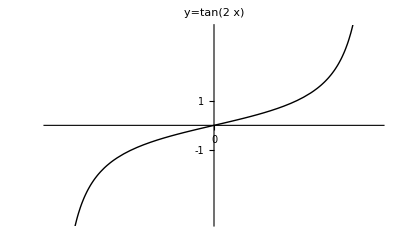

g5.png

```mathematica
Show[
Plot[Tan[2t],{t,-Pi/4,Pi/4},PlotStyle->{Thick,Black},ExclusionsStyle->{Dashed},Exclusions->{t==-Pi/4,t==Pi/4}],
PlotRange->{{-Pi/4,Pi/4},{-4,4}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/8,{k,-8,8}],{-1,1}},PlotLabel->HoldForm[y=Tan[2x]]]
Export["g5.png",%]
```

```mathematica
Solve[3t-Pi/4==2Pi]
```

{{t→(3 π)/4}}

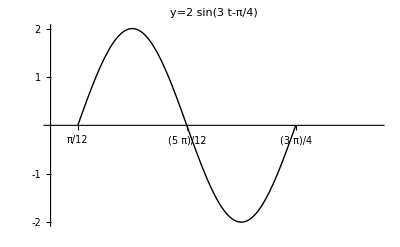

g6.png

```mathematica
Show[
Plot[2Sin[3t-Pi/4],{t,Pi/12,3Pi/4},PlotStyle->{Thick,Black}],
PlotRange->{{0,Pi},{-2,2}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/6+Pi/12,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=2Sin[3t-Pi/4]]]
Export["g6.png",%]
```

```mathematica
3Pi/4-Pi/12
```

(2 π)/3

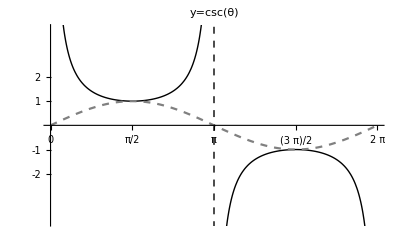

g7.png

```mathematica
Show[
Plot[Csc[t],{t,0,2Pi},PlotStyle->{Thick,Black},Exclusions->{t==Pi,t==2Pi},ExclusionsStyle->Dashed],
Plot[Sin[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,2Pi},{-4,4}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/4,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Csc[θ]]]
Export["g7.png",%]
```

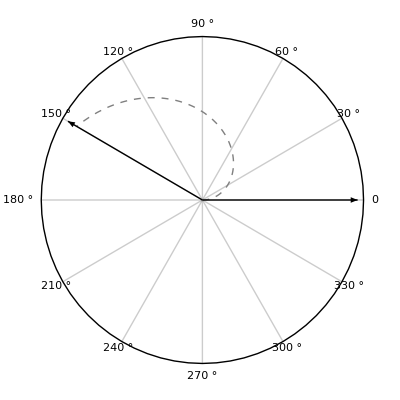

```mathematica
θ=150*Pi/180;
r=0.4;
Show[
PolarPlot[{t/7},{t,0,θ},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,360*Degree-30*Degree,30*Degree}],Automatic},PolarGridLines->{Table[i,{i,0,360*Degree-30*Degree,30*Degree}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ r Cos[θ],r  Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{r ,0}}]}]]
Export["ang1ex.png",%];
```

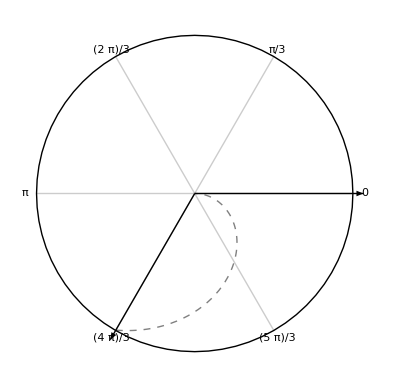

```mathematica
θ=-2*Pi/3;
r=0.28;
Show[PolarPlot[{-t/8},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ r Cos[θ],r Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{r,0}}]}]]
Export["ang2ex.png",%];
```

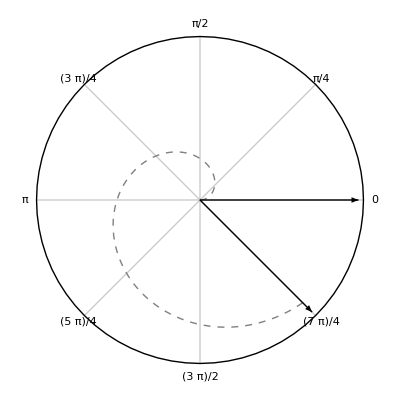

```mathematica
θ=7*Pi/4;
r=1;
Show[PolarPlot[{t/6},{t,0,θ},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ r Cos[θ],r Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{r,0}}]}]]
Export["ang3ex.png",%];
```

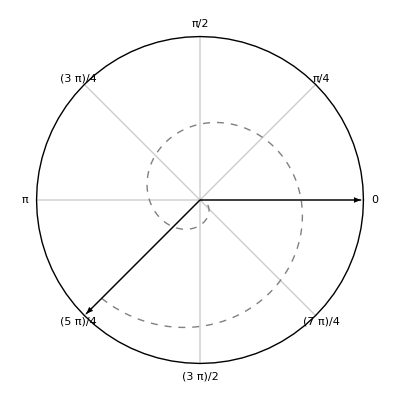

```mathematica
θ=-11*Pi/4;
r=1;
Show[PolarPlot[{-t/10},{t,0,θ},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ r Cos[θ],r Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{r,0}}]}]]
Export["ang4ex.png",%];
```

70 °

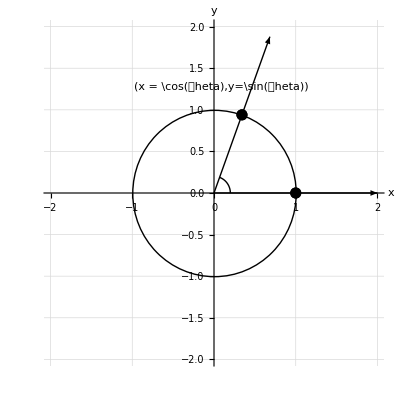

unitcircle.png

```mathematica
SetDirectory[NotebookDirectory[]];
r=1;
θ=70*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style["(x = \cos(\theta),y=\sin(\theta))",Large,Italic],{(r+1) Cos[θ]-0.6,(r+1) Sin[θ]-0.6}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],

PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->{Medium,Italic}]
Export["unitcircle.png",%]
```

```mathematica
zzz
```

{{t→-π/6}}

{{t→(5 π)/6}}

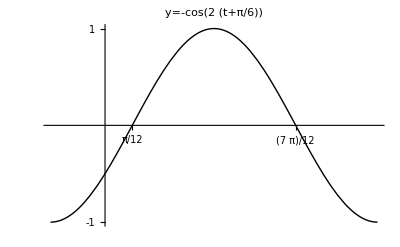

g6-2.png

```mathematica
Solve[2(t+Pi/6)==0]
Solve[2(t+Pi/6)==2Pi]

Show[
Plot[-Cos[2(t+Pi/6)],{t,-Pi/6,5Pi/6},PlotStyle->{Thick,Black}],
PlotRange->{{-Pi/6,5Pi/6},{-1,1}},AxesOrigin->{0,0},
Ticks->{Table[-Pi/6+k Pi/8,{k,-2,10,2}],{-1,1}},PlotLabel->HoldForm[y=-Cos[2(t+Pi/6)]]]
Export["g6-2.png",%]
```

```mathematica
5Pi/6-(-Pi/6)
```

π

```mathematica
Sin[-7Pi/2]
```

1

```mathematica
{Sin[t],Cos[t],Tan[t]}/.t->-Pi/2
```

{-1,0,ComplexInfinity}